# The number of incomplete sweeps at any given time Time to fixation How many sweeps are there going on at any one time in a genome? Specifically, how any are at intermediate frequencies?

Below is the fixation time for an advantageous mutation of additive selective effect s going from frequency p1 to p2 in a population of Ne diploids.

I got this from Otto and Whitlock 2002 (their review of fixation times and probabilities). It comes from Ewans 1979 according to O & W, ask Mike if he has a copy I could borrow. 

TOM! Note that Ewan’s formula is defined in terms of 1, (1+s), (1+2s)
Kimura probs are defined in terms of 1,(1+hs) (1+s).
s should be a half in the time formula, to keep things the same

I don’t currently know how symmetrical the fixation time function is - Is the average fixation time good enough?

```mathematica
tFixArbi[s_,Ne_,p1_,p2_]:=Module[{den,num},
num[x_] =(Exp[2*Ne*s*x ] - 1)*(Exp[2*Ne*s*(1-x) ] - 1);
den[x_]= ((s*x*(1-x))*(Exp[2*Ne*s] -1));
NIntegrate[num[x]/den[x], {x,p1,p2}]]

 tFixIntegrate[shat_, Ne_] :=NIntegrate[tFixArbi[s,Ne,0.2,0.8]* PDF[ExponentialDistribution[1/shat],s], {s, 0,Infinity}]
```

What is the fixation time for a mutation with s = 0.1, in a population of 1000 diploids?

```mathematica
tFixArbi[0.01,10000,0.2,0.8]
tFixIntegrate[0.01,10000]
```

277.259

NIntegrate::inumr: The integrand ((-1+ⅇ^(20000 s (1-x))) (-1+ⅇ^(20000 s x)))/((-1+ⅇ^(20000 s)) s (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

5.44957

```mathematica
ProbabilityDistribution[Sqrt[2]/Pi/(1+x^4),{x,-Infinity,Infinity}]
```

```mathematica
PDF[ExponentialDistribution[1/0.001],0.0001]
```

```mathematica
Integrate[PDF[ExponentialDistribution[1/0.001],x] * 1,{x,0.0001,Infinity}]
PDF[ExponentialDistribution[1/0.001],0.001] * 1
```

0.904837

367.879

```mathematica
NIntegrate[PDF[ExponentialDistribution[1/shat],s] * 1, {s, 0.000000001,0.9999}]
```

Plot the fixation time for a range of selection coefficients, Ne = 1000?

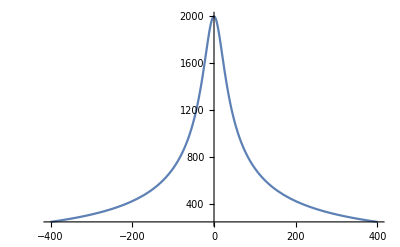

```mathematica
Plot[tFixArbi[Nes/10000,1000,1/20000,1], {Nes,-0.04*10000,0.04*10000}]
```

The above is similar to the plot in O & W, but with the Kimura mutational effect model

What is the fixation time for a mutation with s = 0.0001, in a population of 1000 diploids (Nes = 0.1)? It should be ~2Ne

```mathematica
tFixArbi[0.00001,1000,1/2000,1]
```

1998.99

That’ s pretty close... good job Ewens

NIntegrate::inumr: The integrand ((-1+ⅇ^(20000 s (1-x))) (-1+ⅇ^(20000 s x)))/((-1+ⅇ^(20000 s)) s (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

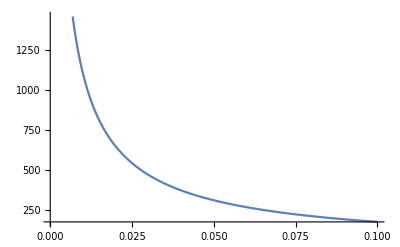

```mathematica
Plot[tFixIntegrate[sh,10000], {sh,0.0001,0.1}]
```

# The number of new sweeping alleles per generation How many sweeps are there going on at any one time in a genome? I will model it in a panmictic Wright-Fisher popn. as follows: Population size = N = Ne The mutation rate per-basepair is μ The proportion of mutations which have their effects drawn from the advantageous DFE is pa The rate of beneficial mutation is thus μ . pa, we’ll call that μ a Beneficial mutations have additive effects on fitness and have selective .7fadvantage s The number of sites in the genome that could mutate to advantageous alleles is ηa The genomic rate of beneficial mutations per generation is: Ua = 2Ne μa ηa Only some of those will fix and will do so with probability 2s, assuming that s > 1/(2N), If there is an exponential distribution of s, the probability density of which is Φ(s) , The rate of beneficial mutations destined to fix which arise each generation is then: Va = ∫ Ua 2s Φ(s) ds With the integral going from 1/(2Ns) to ∞.

```mathematica
Va[N_,ua_,na_, s_]:= 2 N ua na  * 2s
```

```mathematica
VaInt[N_,ua_,na_, sHat_]:= NIntegrate[ 2 N ua na  * 2s * PDF[ExponentialDistribution[1/sHat],s],{s,1/(2N), Infinity}]
```

```mathematica
VaIntTime[N_,ua_,na_, sHat_]:= NIntegrate[ tFixArbi[s,N,0.2, 0.8] * 2 N ua na  * 2s * PDF[ExponentialDistribution[1/sHat],s],{s,1/(2N), Infinity}]
```

What' s the expected number of sweeps starting each generation? Ne = 10^6, pa = 0.0001, μ = 5 x 10^-9, 10^7 non synonymous sites, s_hat = 0.01

```mathematica
VaIntTime[10^4,0.0001* 2.5 10^-7 ,2.5 10^7, 0.01]
VaIntTime[10000,0.001*2.5 10^(-7),25000000, 250/10000]
```

NIntegrate::inumr: The integrand ((-1+ⅇ^(20000 s (1-x))) (-1+ⅇ^(20000 s x)))/((-1+ⅇ^(20000 s)) s (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

68.0826

NIntegrate::inumr: The integrand ((-1+ⅇ^(20000 s (1-x))) (-1+ⅇ^(20000 s x)))/((-1+ⅇ^(20000 s)) s (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

688.171

```mathematica
Va[10^4,0.0001* 2.5 10^-7 ,2.5 10^7, 0.01]
```

0.25

0.25

NIntegrate::inumr: The integrand ((-1+ⅇ^(20000 s (1-x))) (-1+ⅇ^(20000 s x)))/((-1+ⅇ^(20000 s)) s (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

68.0826

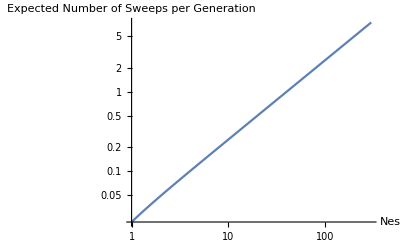

```mathematica
LogLogPlot[VaInt[10000,0.001*2.5 10^(-7),25000000, Nesx/10000],{Nesx,1,300}, AxesLabel->{HoldForm[Nes],HoldForm[Expected Number of Sweeps per Generation]}]
```

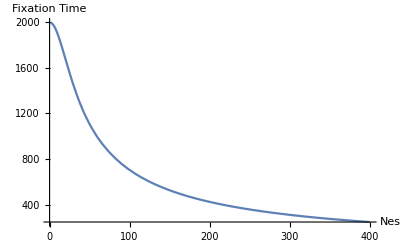

```mathematica
Plot[tFixArbi[Nes/10000,1000,1/20000,1], {Nes,1,0.04*10000}, AxesLabel->{HoldForm[Nes],HoldForm[Fixation Time]}]
```

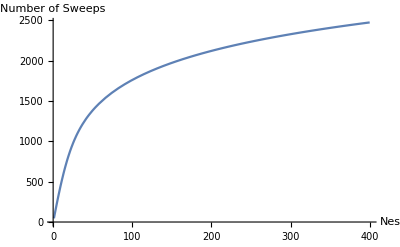

```mathematica
Plot[VaInt[10000,0.001*2.5 10^(-7),25000000, Nes/10000] *tFixArbi[Nes/10000,1000,1/20000,1], {Nes,1,0.04*10000}, AxesLabel->{HoldForm[Nes],HoldForm[Number of Sweeps]}]
```

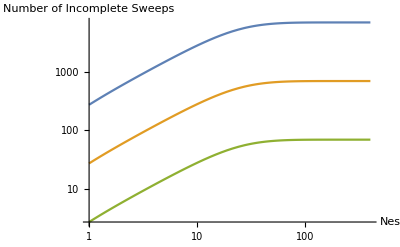

```mathematica
LogLogPlot[ {VaInt[10000,0.01*2.5 10^(-7),25000000, Nes/10000] *tFixArbi[Nes/10000,1000,0.2,0.8] , 
VaInt[10000,0.001*2.5 10^(-7),25000000, Nes/10000] *tFixArbi[Nes/10000,1000,0.2,0.8] ,
VaInt[10000,0.0001*2.5 10^(-7),25000000, Nes/10000] *tFixArbi[Nes/10000,1000,0.2,0.8] },
 {Nes,1,0.04*10000}, AxesLabel->{HoldForm[Nes],HoldForm[Number of Incomplete Sweeps]}]
```

# The expected number of sweeps going on at any time Let’s base it on Drosophila, constant effect size model for the time being; Ne = 10 ^6 - Canonical effective population size for Drosophila μ = 5 x 10^-9 - Estimate from Haag-Liutard et al ηa = 10^7 - This is the mutational target size, pretty conservative for Drosophila 2Nes = 200 - Based on the Campos et al 2017 PNAS estimate To estimate MKalpha, we need the distribution of fitness effects for deleteirous mutations. Let’s assume a typical estimate for Drosophila Shape = 0.3, Mean Nes = 250

```mathematica
Ne= 1 10^4;
mu = 2.5 10^-7;
na = 2.5 10^7;
pa = 0.0001;
s =  100/Ne;

b = 0.3;
sd = 250/Ne;
```

The fixation time for advantageous mutations with constant effects o
f s = 0.01, Nes = 703:

```mathematica
tFixArbi[0.1,10000,1/20000,1]
```

162.577

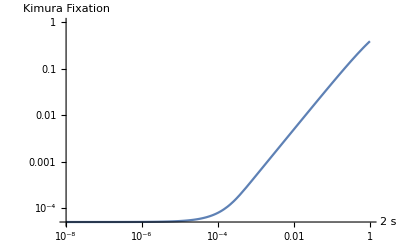

```mathematica
KimuraFixation[s_,N_] := (1 - Exp[-s])/(1 - Exp[-2N s])

LogLogPlot[KimuraFixation[sx/2, 10000],{sx, 0.00000001, 1},AxesLabel->{HoldForm[2s],HoldForm[Kimura Fixation]}]
```

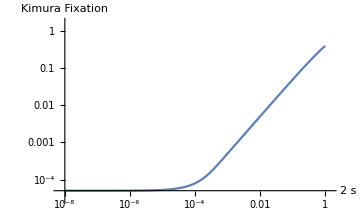

-Graphics-

```mathematica
MKalpha[sa_,pa_, b_,sd_, Ne_] :=Module[{num, denAdv, denDel},
num = pa* KimuraFixation[sa,Ne] ; 
denDel =  NIntegrate[ (1-pa)* KimuraFixation[-1*s,Ne] * PDF[GammaDistribution[b,sd/b],s],{s,0, Infinity}];
num / (num + denDel)]

MKalphaInt[sHat_,pa_, b_,sd_, Ne_] :=Module[{num, denAdv, denDel},
num = NIntegrate[ pa* KimuraFixation[s,Ne] * PDF[ExponentialDistribution[1/sHat],s],{s,1/(2 Ne), Infinity}] ;
denAdv =  NIntegrate[ pa* KimuraFixation[s,Ne] * PDF[ExponentialDistribution[1/sHat],s],{s,0, Infinity}] ; 
denDel =  NIntegrate[ (1-pa)* KimuraFixation[-1*s,Ne] * PDF[GammaDistribution[b,sd/b],s],{s,0, Infinity}];
num / (denAdv + denDel)]

VaInt[10000,0.001*2.5 10^(-7),25000000, 5/10000]
```

VaInt[10000,2.5×10^-10,25000000,1/2000]

```mathematica
tFixArbi[0.01,10000,0,1]
```

1174.1

```mathematica
shat = 0.1
```

0.1

Note that Mathematica uses the following formulation of the Gamma dist.:
    shape = b, scale = mean/shape.

#### Ok, let' s output the average number of sweeps going on in the genome at .7fany given time so that we can plot the results in R

```mathematica
NumberDat01 = Table[ {Nes, VaInt[10000,0.01*2.5 10^(-7),25000000, Nes/10000] *tFixIntegrate[Nes/10000,10000]}, {Nes, 1,250}] ;
Export["Number_of_sweeps_pA0.01.csv",NumberDat01];
```

NIntegrate::inumr: The integrand ((-1+ⅇ^(20000 s (1-x))) (-1+ⅇ^(20000 s x)))/((-1+ⅇ^(20000 s)) s (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
NumberDat001 = Table[ {Nes, VaIntTime[10000,0.001*2.5 10^(-7),25000000, Nes/10000] }, {Nes, 1,250}] ;
Export["Number_of_sweeps_pA0.001.csv",NumberDat001];
```

NIntegrate::inumr: The integrand ((-1+ⅇ^(20000 s (1-x))) (-1+ⅇ^(20000 s x)))/((-1+ⅇ^(20000 s)) s (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
NumberDat0001 = Table[ {Nes, VaInt[10000,0.0001*2.5 10^(-7),25000000, Nes/10000] *tFixArbi[Nes/10000,1000,0.2,0.8]}, {Nes, 1,250}] ;
Export["Number_of_sweeps_pA0.0001.csv",NumberDat0001];
```

NIntegrate::inumr: The integrand ((-1+ⅇ^(20000 s (1-x))) (-1+ⅇ^(20000 s x)))/((-1+ⅇ^(20000 s)) s (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
tFixIntegrate[100/10000,10000]
```

NIntegrate::inumr: The integrand ((-1+ⅇ^(20000 s (1-x))) (-1+ⅇ^(20000 s x)))/((-1+ⅇ^(20000 s)) s (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.2,0.8}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1105.22

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[num$4738132[x]/den$4738132[x],{x,0.2,0.8}]

```mathematica
MKdat01 = Table[ { Nes, MKalpha[Nes/10000,0.01, 0.3,250/10000, 10000]},  {Nes, 1,250}] ;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.9984×10^-15}. NIntegrate obtained 6.30467×10^-6 and 2.43415×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
MKdat001 = Table[ { Nes, MKalpha[Nes/10000,0.001, 0.3,250/10000, 10000]},  {Nes, 1,250}] ;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.9984×10^-15}. NIntegrate obtained 6.36199×10^-6 and 2.45628×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
MKdat0001 = Table[ { Nes, MKalpha[Nes/10000,0.0001, 0.3,250/10000, 10000]},  {Nes, 1,250}] ;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.9984×10^-15}. NIntegrate obtained 6.36772×10^-6 and 2.45849×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
MKdatInt01 = Table[ { Nes, MKalphaInt[Nes/10000,0.01, 0.3,250/10000, 10000]},  {Nes, 1,250}] ;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.9984×10^-15}. NIntegrate obtained 6.30467×10^-6 and 2.43415×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
MKdatInt001 = Table[ { Nes, MKalphaInt[Nes/10000,0.001, 0.3,250/10000, 10000]},  {Nes, 1,250}] ;
```

```mathematica
MKdatInt0001 = Table[ { Nes, MKalphaInt[Nes/10000,0.0001, 0.3,250/10000, 10000]},  {Nes, 1,250}] ;
```

```mathematica
Export["MKalpha_pA0.01.csv",MKdat01];
Export["MKalpha_pA0.001.csv",MKdat001];
Export["MKalpha_pA0.0001.csv",MKdat0001];
```

```mathematica
Export["MKalphaInt_pA0.01.csv",MKdatInt01];
Export["MKalphaInt_pA0.001.csv",MKdatInt001];
Export["MKalphaInt_pA0.0001.csv",MKdatInt0001];
```

```mathematica
MKalpha[1/10000,0.0001, 0.3,250/10000, 10000]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.9984×10^-15}. NIntegrate obtained 6.36772×10^-6 and 2.45849×10^-10 for the integral and error estimates.

0.00181284

```mathematica
MKalphaInt[1/10000,0.0001, 0.3,250/10000, 10000]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.9984×10^-15}. NIntegrate obtained 6.36772×10^-6 and 2.45849×10^-10 for the integral and error estimates.

0.00154703